## Core parameters

```mathematica
α=1;β=2;γ=.;
q1=2;q2=3;
```

```mathematica
cols=ColorData[97,"ColorList"]⟦{2,1,3}⟧
```

{RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.560181, 0.691569, 0.194885]}

## Dynamic γ

```mathematica
G=0.1;ginit=0.4;
sampleinits=Table[i,{i,0.0,1.0,0.05}];
ginits=Table[i,{i,0,1.0,0.05}];
```

```mathematica
dy1[y1_,γ_]:=y1 (1-y1)(((1-γ) q1/(q1+q2)+γ α y1^β/(y1^β+(1-y1)^β)) q1 -( (1-γ) q2/(q1+q2)+γ α (1-y1)^β/((1-y1)^β+y1^β)) q2);
```

```mathematica
sol[y1init_,ginit_,Gon_]:=NDSolve[{
y1'[t]==dy1[y1[t],g[t]],
g'[t]==
If[Gon==True,
If[
Sign[dy1[y1[t],g[t]]]>0,-G,
If[Sign[dy1[y1[t],g[t]]]<0,G,0]],
0],
y1[0]==y1init,g[0]==ginit,WhenEvent[g[t]<0,g[t]->0],WhenEvent[g[t]>1,g[t]->1]},{y1,g},{t,0,100}];
```

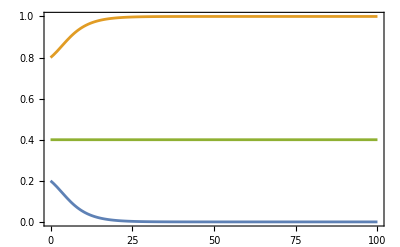

```mathematica
Plot[Evaluate[{y1[t],1-y1[t],g[t]}/.sol[0.8,0.4,False]],{t,0,100},PlotStyle->Join[cols,{Gray}],Frame->True,FrameStyle->Directive[Thickness[0.003]]]
```

```mathematica
Manipulate[Plot[Evaluate[{y1[t],1-y1[t],g[t]}/.sol[yinit,0.4,True]],{t,0,2},PlotStyle->Join[cols,{Gray}],Frame->True,FrameStyle->Directive[Thickness[0.003]],PlotRange->{Automatic,{-0.01,1.01}}],{yinit,0,1,0.01}]
```

General::munfl: -1.16034×10^-305 2.645×10^-12 is too small to represent as a normalized machine number; precision may be lost.

```mathematica
ϵ=10^-5;
```

```mathematica
staticgamma={};
For[j=1,j≤Length[ginits],j++,
For[i=1,i≤Length[sampleinits],i++,
meandata=Mean[Table[Evaluate[{y1[t],1-y1[t],g[t]}/.sol[sampleinits⟦i⟧,ginits⟦j⟧,False]],{t,0,100}]⟦-10;;⟧]⟦1,1⟧;
AppendTo[staticgamma,{{ginits⟦j⟧,sampleinits⟦i⟧,If[Abs[meandata-0]<ϵ||Abs[meandata-1]<ϵ,"Fixed","Polymorphic"]}}]
]
]
```

```mathematica
dynamicgamma={};
For[j=1,j≤Length[ginits],j++,
For[i=1,i≤Length[sampleinits],i++,
meandata=Mean[Table[Evaluate[{y1[t],1-y1[t],g[t]}/.sol[sampleinits⟦i⟧,ginits⟦j⟧,True]],{t,0,100}]⟦-10;;⟧]⟦1,1⟧;
AppendTo[dynamicgamma,{{ginits⟦j⟧,sampleinits⟦i⟧,If[Abs[meandata-0]<ϵ||Abs[meandata-1]<ϵ,"Fixed","Polymorphic"]}}]
]
]
```

General::munfl: -3.59887×10^-306 2.66809×10^-12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -6.90046×10^-301 2.65388×10^-12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
ListDensityPlot[Flatten[staticgamma,1]/.{"Fixed"->0,"Polymorphic"->1},PlotRange->All,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]}]
```

-Graphics-

```mathematica
ListDensityPlot[Flatten[dynamicgamma,1]/.{"Fixed"->0,"Polymorphic"->1},PlotRange->All,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]}]
```

-Graphics-

ReplaceAll::reps: {sol[0.,False]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

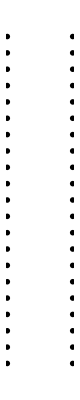

```mathematica
Table[{Plot[Evaluate[{y1[t],1-y1[t],g[t]}/.sol[sampleinits⟦i⟧,False]],{t,0,100},PlotStyle->Join[cols,{Gray}],Frame->True,FrameStyle->Directive[Thickness[0.003]],PlotRange->{Automatic,{-0.01,1.01}}],
Plot[Evaluate[{y1[t],1-y1[t],g[t]}/.sol[sampleinits⟦i⟧,True]],{t,0,100},PlotStyle->Join[cols,{Gray}],Frame->True,FrameStyle->Directive[Thickness[0.003]],PlotRange->{Automatic,{-0.01,1.01}}]},{i,1,Length[sampleinits],1}]//GraphicsGrid
```